```mathematica
x=.
```

```mathematica
u=.
```

```mathematica
p=Import["C:\\Users\\deber\\GeometricTools\\GTL\\Internal\\UnitTests\\Mathematics\\NumericalMethods\\RootFinders\\Coefficients.txt","List"]
```

{0.341875,1.07275,-0.416613,-3.29617,0.282222,4.07804,-1.72063,-2.27743,2.48383,-0.368295,-0.83965,0.727136,-0.298774,0.0676107,-0.0075269}

```mathematica
q=p[[15]]
```

-0.0075269

```mathematica
For[i=14,i≥0,i--,q=p[[i]]+x*q]
```

```mathematica
u=q[[2]]/x
```

0.341875+x (1.07275+x (-0.416613+x (-3.29617+x (0.282222+x (4.07804+x (-1.72063+x (-2.27743+x (2.48383+x (-0.368295+x (-0.83965+x (0.727136+x (-0.298774+(0.0676107-0.0075269 x) x))))))))))))

```mathematica
r=NSolve[SetPrecision[u==0,64],x,Reals,64]
```

{{x→-0.664240464156974313965685501967635997726228032547090556623},{x→0.86338649912050745446360085778283331178597231623873866699771977}}

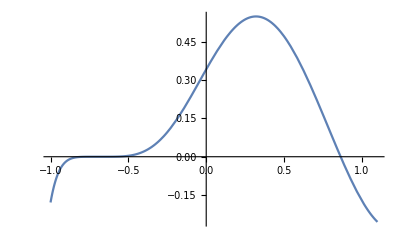

```mathematica
Plot[u,{x,-1,1.1}]
```

```mathematica
x=r[[1]][[All,2]][[1]]
```

-0.664240464156974313965685501967635997726228032547090556623

```mathematica
u
```

-5.55112×10^-17

```mathematica
x=.
```

```mathematica
RootIntervals[u]
```

{{{-19069/28672,-19039/28672},{167/224,197/224}},{{1},{1}}}

```mathematica
x=r[[2]][[All,2]][[1]]
```

0.86338649912050745446360085778283331178597231623873866699771977

```mathematica
u
```

-1.11022×10^-16